```mathematica
(*setup global parameters*)
ClearAll;
nI =16;
nJ =1;
nK = 1;
g0Scale= .1;
w0  = 1.67;
g0 = 0;
ν0= w0;
r0Scale = .0001;
numBosons=1000;
highestFreq  = 200*w0;
tf = .001;
(*need to parse files for i j k index*)
(*input file_2_4_463*)
(*output {2,4,463} where elements are integers*)
parserIJK=(ToExpression/@
StringSplit[StringReplace[StringCases[#2,RegularExpression[#1<>"(_\\d{1,3}){3,3}$"]][[1]],#1->""],"_"])&;
(*Epsilon: probability amplitude cutoff*)
(*Gamma: Spectral intensity of the resevior*)
(*Delta: cavity and emitter frequency spacing*)
paramEpsilon[i_] :=  g0Scale*ⅇ^((-Log[numBosons])/nI i);
paramDelta[j_] :=If[j==-1,0,Abs[w0(1-  ⅇ^(Log[2]/nJ j))]];
paramLargestFrequency[j_]:=highestFreq*ⅇ^(Log[20]/nJ j);
paramGamma[k_] := r0Scale*ⅇ^(Log[g0Scale/r0Scale]/nK k);
(*make global map that says if parameter is i,j,k, or is default*)
paramMap[i_,j_,k_]:= <|"ℊ"->g0,"ω"->i,"ν"->ν0,"ϵ"->3,"δ"->-1,"ℱ"->1,"γ"->2,"𝓉"->tf|>;
printParams[i_,j_,k_]:=TemplateApply["ϵ-> <*paramEpsilon[#ϵ]*>,  ℊ_0-> `ℊ`, ω_0-> <*#ω+paramDelta[#δ]*>,\n δ-> <*paramDelta[#δ]*>, γ-> <*paramGamma[#γ]*>,1/Δt-> <*paramLargestFrequency[#ℱ]*>",paramMap[i,j,k]];
(*file paths *)
base =  "/home/ethan/curr_proj";
pythonOut = base<>"/python_out";
codeOut = base<>"/code_out_scale_time_2";
mathematicaOut = base <> "/mathematica_out";
(*important files*)
adaptiveSpin = base<>"/adaptive_spin";
generateSystem = base <> "/generate_energies.py";
configFile = base <> "/parameters.conf";
RunProcess[{"mkdir",codeOut}]
```

<|ExitCode→1,StandardOutput→,StandardError→/usr/bin/mkdir: cannot create directory '/home/ethan/curr_proj/code_out_scale_time_2': File exists
|>

```mathematica
(*generate system files via python*)
pythonArg=
Module[{i,j,k,outputDir=pythonOut,pythonFile=generateSystem,params={},w0=w0},
For[i = 0,i<nI, i++,
For[j = 0, j < nJ, j++,
For[k=0, k< nK, k++,
tmpW0 = w0+paramDelta[j];
tmpW0 = <|"a" -> tmpW0|>;
params= Append[params, {"python" ,pythonFile,TemplateApply[ "--w0=<*w0*#ω*>",paramMap[i,j,k]],
TemplateApply[ "--fastest_time_scale=<*(paramLargestFrequency[#ℱ])^-1*>",paramMap[i,j,k]],
TemplateApply[ "--g0=`ℊ`",paramMap[i,j,k]],
TemplateApply[ "--v0=<*#ν*>",paramMap[i,j,k]],
TemplateApply[ "--gamma=<*paramGamma[#γ]*>",paramMap[i,j,k]],
StringTemplate["--emitter_out=`out`/emitter_out_`i`_`j`_`k`"][<|"out"->outputDir,"i"->i,"j"->j,"k"->k|>],
StringTemplate["--bosons_out=`out`/bosons_out_`i`_`j`_`k`"][<|"out"->outputDir,"i"->i,"j"->j,"k"->k|>],
StringTemplate["-N=`n`"][<|"n"->numBosons|>] } ];
];];];
params
];
RunProcess[{"rm","-r",pythonOut}];
Pause[1];
RunProcess[{"mkdir",pythonOut}];
prcc=StartProcess/@pythonArg;
```

```mathematica
ProcessInformation/@prcc
```

```mathematica
(*pass parameters to adaptive_spin*)
codeArg =Module[{i,j,k,executablePath = adaptiveSpin,codeOut =codeOut,pythonOut=pythonOut, outputFilePath,params={},val,conf=configFile},
For[i = 0, i <nI,i++,
For[j = 0, j < nJ, j++,
For [k = 0, k < nK, k++,
outputFilePath = StringTemplate[codeOut<>"/run_`a`_`b`_`c`"]
[<|"a"->i, "b"->j,"c"->k |>];
params = Append[params,
{executablePath,
TemplateApply["--time_end=`𝓉`",paramMap[i,j,k]],
TemplateApply["--cutoff=<*paramEpsilon[#ϵ]*>",paramMap[i,j,k]],
TemplateApply["--largest_frequency=<*paramLargestFrequency[#ℱ]*>",paramMap[i,j,k]],
 StringTemplate["--atom_p=`out`/emitter_out_`a`_`b`_`c`"][<|"out"->pythonOut,"a"->i,"b"->j,"c"->k|>],
StringTemplate["--mode_p=`out`/bosons_out_`a`_`b`_`c`"][<|"out"->pythonOut,"a"->i,"b"->j,"c"->k|>],
StringTemplate["--output_file=`a`"][<|"a"->outputFilePath|>],StringTemplate["--config=`a`"][<|"a"->conf|>]}];
];];];
params
];
processes=StartProcess/@codeArg;
```

```mathematica
ProcessStatus/@processes
```

{Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished}

```mathematica
dataCollection = Module[{mathematicaOut= mathematicaOut,codeOut=codeOut,pythonOut=pythonOut,tmpFileList,outputFilePaths,codeTable,spectralTable,suffixList},
tmpFileList = mathematicaOut<>"/tmpfiles";
Run["ls "<> codeOut<>  " > " <> tmpFileList];
tmpFileList = Import[tmpFileList,"String"];
Pause[.01];
outputFilePaths=StringCases[tmpFileList,RegularExpression["run(_\\d{1,3}){3,3}"]];
suffixList = StringCases[#,RegularExpression["(_\\d{1,3}){3,3}"]]&/@outputFilePaths;
codeTable=({Import[codeOut<>"/"<>#,"Table"],parserIJK["run",#]})&/@outputFilePaths;
tmpFileList = mathematicaOut<>"/tmpfiles";
Run["ls "<> pythonOut<>  " > " <> tmpFileList];
tmpFileList = Import[tmpFileList,"String"];
Pause[.01];
bosonPaths=StringCases[tmpFileList,RegularExpression["bosons_out"<>#]][[1]]&/@suffixList;
emitterPaths = StringCases[tmpFileList,RegularExpression["emitter_out"<>#]][[1]]&/@suffixList;
spectralTable={Import[pythonOut<>"/"<>#,"Table"]&/@bosonPaths,Import[pythonOut<>"/"<>#,"Table"]&/@emitterPaths,parserIJK["bosons_out",#]&/@bosonPaths};
{codeTable,spectralTable}
];
Length[dataCollection[[2]][[3]]]
```

16

```mathematica
pltList=
Module[{i,pmap, dynamicsOutput,spectralInput,q,params,pUp,pDown,pltTmp,plts={},ωSpectra,ωPlt,ℊSpectra,lineStyle,lineOmega,sortedPlts=Table[{},{i,1,nI},{j,1,nJ},{k,1,nK}]},
For[i = 1, i ≤Length[dataCollection[[1]]],i++,
dynamicsOutput = dataCollection[[1]][[i]][[1]];
spectralInput =  dataCollection[[2]][[1]][[i]];
q =  dataCollection[[1]][[i]][[2]];
pmap = paramMap[q[[1]],q[[2]],q[[3]]];
params =printParams[q[[1]],q[[2]],q[[3]]];
pUp = Table[{dynamicsOutput[[j]][[1]],dynamicsOutput[[j]][[2]]},{j,1,Length[dynamicsOutput]-2}];
pDown = Table[{dynamicsOutput[[j]][[1]],dynamicsOutput[[j]][[3]]},{j,1,Length[dynamicsOutput]-2}];
ωSpectra = Table[spectralInput[[j]][[1]],{j,1,Length[spectralInput]}];
ProgressIndicator[i,{0,Length[dataCollection[[1]]]}];
ℊSpectra =  Table[spectralInput[[j]][[2]],{j,1,Length[spectralInput]}];
lineStyle={Red,Dashed};
lineOmega=Line[{{w0,0},{w0,100}}];
ωPlt=
{Histogram[ωSpectra,{.01},Epilog->{Directive[lineStyle],lineOmega},PlotLabel->TemplateApply["Histogram of modes as a function of frequency \n(red line is ω_0 = <*#ω*> (ev/ℏ) \n",pmap]<>printParams[q[[1]],q[[2]],q[[3]]],AxesLabel->{"Frequency (ev/ℏ)","Count"},ImageSize->Medium],
ListPlot[Table[{ωSpectra[[i]],ℊSpectra[[i]]},{i,1,Length[ωSpectra]}],PlotLabel->TemplateApply["coupling as a function of frequency\n (red line is ω_0 = <*#ω*> (ev/ℏ) \n",pmap]<>printParams[q[[1]],q[[2]],q[[3]]],AxesLabel->{"Frequency (ev/ℏ)","Coupling Strength"},ImageSize->Medium,Epilog->{Directive[lineStyle],lineOmega},PlotRange->Full]};

pltTmp = {{ListPlot[{pUp,pDown},PlotLabel->"Probability of Emitter vs Time (ℏ = eV = 1) \n " <> params,AxesLabel->{"time (ℏ/eV ~ 6*10^-16)"},PlotLegends->{"e","g"},ImageSize->Medium],
ListLogPlot[{pUp,pDown},PlotLabel->"Probability of Emitter vs Time (ℏ = eV = 1)\n" <> params,AxesLabel->{"time (ℏ/eV ~ 6*10^-16)"},PlotLegends->{"e","g"},ImageSize->Medium]},q};
sortedPlts[[q[[1]]+1]][[q[[2]]+1]][[q[[3]]+1]]={pltTmp,ωPlt};
];
sortedPlts
];
```

```mathematica
Manipulate[{pltList[[i]][[j]][[k]][[1]][[1]][[2]],pltList[[i]][[j]][[k]][[2]][[2]]},{i,1,nI,1},{j,1,nJ,1},{k,1,nK,1}]
```

$Aborted

Part::partd: Part specification pltList⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

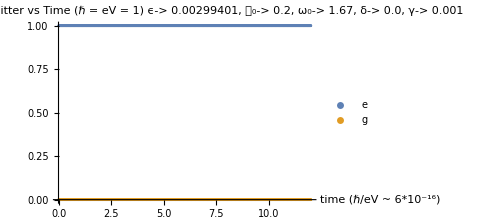

```mathematica
pltList[[1]][[1]][[1]][[1]][[1]]
```

```mathematica
{#[[1]],#[[2]]}&/@dataCollection[[1]][[1]]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

{{0.01,0.996102},{0.02,0.900936},{0.03,0.729273},{0.04,0.589017},{0.05,0.487775},{0.06,0.580591},{0.07,0.482783},{0.08,0.577979},{0.09,0.480783},{0.1,0.576228},{0.11,0.479443},{0.12,0.575054},{0.13,0.478544},{0.14,0.574265},{0.15,0.477941},{0.16,0.573735},{0.17,0.477535},{0.18,0.573379},{0.19,0.477263},{0.2,0.57314},{0.21,0.47708},{0.22,0.572979},{0.23,0.476957},{0.24,0.572871},{0.25,0.476875},{0.26,0.572798},{0.27,0.476819},{0.28,0.57275},{0.29,0.476782},{0.3,0.572717},{0.31,0.476757},{0.32,0.572695},{0.33,0.47674},{0.34,0.57268},{0.35,0.476728},{0.36,0.57267},{0.37,0.476721},{0.38,0.572663},{0.39,0.476716},{0.4,0.572659},{0.41,0.476712},{0.42,0.572656},{0.43,0.47671},{0.44,0.572654},{0.45,0.476708},{0.46,0.572652},{0.47,0.476707},{0.48,0.572651},{0.49,0.476706},{0.5,0.572651},{0.51,0.476706},{0.52,0.57265},{0.53,0.476706},{0.54,0.57265},{0.55,0.476705},{0.56,0.57265},{0.57,0.476705},{0.58,0.57265},{0.59,0.476705},{0.6,0.57265},{0.61,0.476705},{0.62,0.57265},{0.63,0.476705},{0.64,0.572649},{0.65,0.476705},{0.66,0.572649},{0.67,0.476705},{0.68,0.572649},{0.69,0.476705},{0.7,0.572649},{0.71,0.476705},{0.72,0.572649},{0.73,0.476705},{0.74,0.572649},{0.75,0.476705},{0.76,0.572649},{0.77,0.476705},{0.78,0.572649},{0.79,0.476705},{0.8,0.572649},{0.81,0.476705},{0.82,0.572649},{0.83,0.476705},{0.84,0.572649},{0.85,0.476705},{0.86,0.572649},{0.87,0.476705},{0.88,0.572649},{0.89,0.476705},{0.9,0.572649},{0.91,0.476705},{0.92,0.572649},{0.93,0.476705},{0.94,0.572649},{0.95,0.476705},{0.96,0.572649},{0.97,0.476705},{0.98,0.572649},{0.99,0.476705},{1,0.572649},{1.01,0.476705},{1.02,0.572649},{1.03,0.476705},{1.04,0.572649},{1.05,0.476705},{1.06,0.572649},{1.07,0.476705},{1.08,0.572649},{1.09,0.476705},{1.1,0.572649},{1.11,0.476705},{1.12,0.572649},{1.13,0.476705},{1.14,0.572649},{1.15,0.476705},{1.16,0.572649},{1.17,0.476705},{1.18,0.572649},{1.19,0.476705},{1.2,0.572649},{1.21,0.476705},{1.22,0.572649},{1.23,0.476705},{1.24,0.572649},{1.25,0.476705},{1.26,0.572649},{1.27,0.476705},{1.28,0.572649},{1.29,0.476705},{1.3,0.572649},{1.31,0.476705},{1.32,0.572649},{1.33,0.476705},{1.34,0.572649},{1.35,0.476705},{1.36,0.572649},{1.37,0.476705},{1.38,0.572649},{1.39,0.476705},{1.4,0.572649},{1.41,0.476705},{1.42,0.572649},{1.43,0.476705},{1.44,0.572649},{1.45,0.476705},{1.46,0.572649},{1.47,0.476705},{1.48,0.572649},{1.49,0.476705},{1.5,0.572649},{1.51,0.476705},{1.52,0.572649},{1.53,0.476705},{1.54,0.572649},{1.55,0.476705},{1.56,0.572649},{1.57,0.476705},{1.58,0.572649},{1.59,0.476705},{1.6,0.572649},{1.61,0.476705},{1.62,0.572649},{1.63,0.476705},{1.64,0.572649},{1.65,0.476705},{1.66,0.572649},{1.67,0.476705},{1.68,0.572649},{1.69,0.476705},{1.7,0.572649},{1.71,0.476705},{1.72,0.572649},{1.73,0.476705},{1.74,0.572649},{1.75,0.476705},{1.76,0.572649},{1.77,0.476705},{1.78,0.572649},{1.79,0.476705},{1.8,0.572649},{1.81,0.476705},{1.82,0.572649},{1.83,0.476705},{1.84,0.572649},{1.85,0.476705},{1.86,0.572649},{1.87,0.476705},{1.88,0.572649},{1.89,0.476705},{1.9,0.572649},{1.91,0.476705},{1.92,0.572649},{1.93,0.476705},{1.94,0.572649},{1.95,0.476705},{1.96,0.572649},{1.97,0.476705},{1.98,0.572649},{1.99,0.476705},{2,0.572649},{2.01,0.476705},{2.02,0.572649},{2.03,0.476705},{2.04,0.572649},{2.05,0.476705},{2.06,0.572649},{2.07,0.476705},{2.08,0.572649},{2.09,0.476705},{2.1,0.572649},{2.11,0.476705},{2.12,0.572649},{2.13,0.476705},{2.14,0.572649},{2.15,0.476705},{2.16,0.572649},{2.17,0.476705},{2.18,0.572649},{2.19,0.476705},{2.2,0.572649},{2.21,0.476705},{2.22,0.572649},{2.23,0.476705},{2.24,0.572649},{2.25,0.476705},{2.26,0.572649},{2.27,0.476705},{2.28,0.572649},{2.29,0.476705},{2.3,0.572649},{2.31,0.476705},{2.32,0.572649},{2.33,0.476705},{2.34,0.572649},{2.35,0.476705},{2.36,0.572649},{2.37,0.476705},{2.38,0.572649},{2.39,0.476705},{2.4,0.572649},{2.41,0.476705},{2.42,0.572649},{2.43,0.476705},{2.44,0.572649},{2.45,0.476705},{2.46,0.572649},{2.47,0.476705},{2.48,0.572649},{2.49,0.476705},{2.5,0.572649},{2.51,0.476705},{2.52,0.572649},{2.53,0.476705},{2.54,0.572649},{2.55,0.476705},{2.56,0.572649},{2.57,0.476705},{2.58,0.572649},{2.59,0.476705},{2.6,0.572649},{2.61,0.476705},{2.62,0.572649},{2.63,0.476705},{2.64,0.572649},{2.65,0.476705},{2.66,0.572649},{2.67,0.476705},{2.68,0.572649},{2.69,0.476705},{2.7,0.572649},{2.71,0.476705},{2.72,0.572649},{2.73,0.476705},{2.74,0.572649},{2.75,0.476705},{2.76,0.572649},{2.77,0.476705},{2.78,0.572649},{2.79,0.476705},{2.8,0.572649},{2.81,0.476705},{2.82,0.572649},{2.83,0.476705},{2.84,0.572649},{2.85,0.476705},{2.86,0.572649},{2.87,0.476705},{2.88,0.572649},{2.89,0.476705},{2.9,0.572649},{2.91,0.476705},{2.92,0.572649},{2.93,0.476705},{2.94,0.572649},{2.95,0.476705},{2.96,0.572649},{2.97,0.476705},{2.98,0.572649},{2.99,0.476705},{3,0.572649},{3.01,0.476705},{3.02,0.572649},{3.03,0.476705},{3.04,0.572649},{3.05,0.476705},{3.06,0.572649},{3.07,0.476705},{3.08,0.572649},{3.09,0.476705},{3.1,0.572649},{3.11,0.476705},{3.12,0.572649},{3.13,0.476705},{3.14,0.572649},{3.15,0.476705},{3.16,0.572649},{3.17,0.476705},{3.18,0.572649},{3.19,0.476705},{3.2,0.572649},{3.21,0.476705},{3.22,0.572649},{3.23,0.476705},{3.24,0.572649},{3.25,0.476705},{3.26,0.572649},{3.27,0.476705},{3.28,0.572649},{3.29,0.476705},{3.3,0.572649},{3.31,0.476705},{3.32,0.572649},{3.33,0.476705},{3.34,0.572649},{3.35,0.476705},{3.36,0.572649},{3.37,0.476705},{3.38,0.572649},{3.39,0.476705},{3.4,0.572649},{3.41,0.476705},{3.42,0.572649},{3.43,0.476705},{3.44,0.572649},{3.45,0.476705},{3.46,0.572649},{3.47,0.476705},{3.48,0.572649},{3.49,0.476705},{3.5,0.572649},{3.51,0.476705},{3.52,0.572649},{3.53,0.476705},{3.54,0.572649},{3.55,0.476705},{3.56,0.572649},{3.57,0.476705},{3.58,0.572649},{3.59,0.476705},{3.6,0.572649},{3.61,0.476705},{3.62,0.572649},{3.63,0.476705},{3.64,0.572649},{3.65,0.476705},{3.66,0.572649},{3.67,0.476705},{3.68,0.572649},{3.69,0.476705},{3.7,0.572649},{3.71,0.476705},{3.72,0.572649},{3.73,0.476705},{3.74,0.572649},{3.75,0.476705},{3.76,0.572649},{3.77,0.476705},{3.78,0.572649},{3.79,0.476705},{3.8,0.572649},{3.81,0.476705},{3.82,0.572649},{3.83,0.476705},{3.84,0.572649},{3.85,0.476705},{3.86,0.572649},{3.87,0.476705},{3.88,0.572649},{3.89,0.476705},{3.9,0.572649},{3.91,0.476705},{3.92,0.572649},{3.93,0.476705},{3.94,0.572649},{3.95,0.476705},{3.96,0.572649},{3.97,0.476705},{3.98,0.572649},{3.99,0.476705},{4,0.572649},{4.01,0.476705},{4.02,0.572649},{4.03,0.476705},{4.04,0.572649},{4.05,0.476705},{4.06,0.572649},{4.07,0.476705},{4.08,0.572649},{4.09,0.476705},{4.1,0.572649},{4.11,0.476705},{4.12,0.572649},{4.13,0.476705},{4.14,0.572649},{4.15,0.476705},{4.16,0.572649},{4.17,0.476705},{4.18,0.572649},{4.19,0.476705},{4.2,0.572649},{4.21,0.476705},{4.22,0.572649},{4.23,0.476705},{4.24,0.572649},{4.25,0.476705},{4.26,0.572649},{4.27,0.476705},{4.28,0.572649},{4.29,0.476705},{4.3,0.572649},{4.31,0.476705},{4.32,0.572649},{4.33,0.476705},{4.34,0.572649},{4.35,0.476705},{4.36,0.572649},{4.37,0.476705},{4.38,0.572649},{4.39,0.476705},{4.4,0.572649},{4.41,0.476705},{4.42,0.572649},{4.43,0.476705},{4.44,0.572649},{4.45,0.476705},{4.46,0.572649},{4.47,0.476705},{4.48,0.572649},{4.49,0.476705},{4.5,0.572649},{4.51,0.476705},{4.52,0.572649},{4.53,0.476705},{4.54,0.572649},{4.55,0.476705},{4.56,0.572649},{4.57,0.476705},{4.58,0.572649},{4.59,0.476705},{4.6,0.572649},{4.61,0.476705},{4.62,0.572649},{4.63,0.476705},{4.64,0.572649},{4.65,0.476705},{4.66,0.572649},{4.67,0.476705},{4.68,0.572649},{4.69,0.476705},{4.7,0.572649},{4.71,0.476705},{4.72,0.572649},{4.73,0.476705},{4.74,0.572649},{4.75,0.476705},{4.76,0.572649},{4.77,0.476705},{4.78,0.572649},{4.79,0.476705},{4.8,0.572649},{4.81,0.476705},{4.82,0.572649},{4.83,0.476705},{4.84,0.572649},{4.85,0.476705},{4.86,0.572649},{4.87,0.476705},{4.88,0.572649},{4.89,0.476705},{4.9,0.572649},{4.91,0.476705},{4.92,0.572649},{4.93,0.476705},{4.94,0.572649},{4.95,0.476705},{4.96,0.572649},{4.97,0.476705},{4.98,0.572649},{4.99,0.476705},{5,0.572649},{5.01,0.476705},{5.02,0.572649},{5.03,0.476705},{5.04,0.572649},{5.05,0.476705},{5.06,0.572649},{5.07,0.476705},{5.08,0.572649},{5.09,0.476705},{5.1,0.572649},{5.11,0.476705},{5.12,0.572649},{5.13,0.476705},{5.14,0.572649},{5.15,0.476705},{5.16,0.572649},{5.17,0.476705},{5.18,0.572649},{5.19,0.476705},{5.2,0.572649},{5.21,0.476705},{5.22,0.572649},{5.23,0.476705},{5.24,0.572649},{5.25,0.476705},{5.26,0.572649},{5.27,0.476705},{5.28,0.572649},{5.29,0.476705},{5.3,0.572649},{5.31,0.476705},{5.32,0.572649},{5.33,0.476705},{5.34,0.572649},{5.35,0.476705},{5.36,0.572649},{5.37,0.476705},{5.38,0.572649},{5.39,0.476705},{5.4,0.572649},{5.41,0.476705},{5.42,0.572649},{5.43,0.476705},{5.44,0.572649},{5.45,0.476705},{5.46,0.572649},{5.47,0.476705},{5.48,0.572649},{5.49,0.476705},{5.5,0.572649},{5.51,0.476705},{5.52,0.572649},{5.53,0.476705},{5.54,0.572649},{5.55,0.476705},{5.56,0.572649},{5.57,0.476705},{5.58,0.572649},{5.59,0.476705},{5.6,0.572649},{5.61,0.476705},{5.62,0.572649},{5.63,0.476705},{5.64,0.572649},{5.65,0.476705},{5.66,0.572649},{5.67,0.476705},{5.68,0.572649},{5.69,0.476705},{5.7,0.572649},{5.71,0.476705},{5.72,0.572649},{5.73,0.476705},{5.74,0.572649},{5.75,0.476705},{5.76,0.572649},{5.77,0.476705},{5.78,0.572649},{5.79,0.476705},{5.8,0.572649},{5.81,0.476705},{5.82,0.572649},{5.83,0.476705},{5.84,0.572649},{5.85,0.476705},{5.86,0.572649},{5.87,0.476705},{5.88,0.572649},{5.89,0.476705},{5.9,0.572649},{5.91,0.476705},{5.92,0.572649},{5.93,0.476705},{5.94,0.572649},{5.95,0.476705},{5.96,0.572649},{5.97,0.476705},{5.98,0.572649},{5.99,0.476705},{6,0.572649},{6.01,0.476705},{6.02,0.572649},{6.03,0.476705},{6.04,0.572649},{6.05,0.476705},{6.06,0.572649},{6.07,0.476705},{6.08,0.572649},{6.09,0.476705},{6.1,0.572649},{6.11,0.476705},{6.12,0.572649},{6.13,0.476705},{6.14,0.572649},{6.15,0.476705},{6.16,0.572649},{6.17,0.476705},{6.18,0.572649},{6.19,0.476705},{6.2,0.572649},{6.21,0.476705},{6.22,0.572649},{6.23,0.476705},{6.24,0.572649},{6.25,0.476705},{6.26,0.572649},{6.27,0.476705},{6.28,0.572649},{6.29,0.476705},{6.3,0.572649},{6.31,0.476705},{6.32,0.572649},{6.33,0.476705},{6.34,0.572649},{6.35,0.476705},{6.36,0.572649},{6.37,0.476705},{6.38,0.572649},{6.39,0.476705},{6.4,0.572649},{6.41,0.476705},{6.42,0.572649},{6.43,0.476705},{6.44,0.572649},{6.45,0.476705},{6.46,0.572649},{6.47,0.476705},{6.48,0.572649},{6.49,0.476705},{6.5,0.572649},{6.51,0.476705},{6.52,0.572649},{6.53,0.476705},{6.54,0.572649},{6.55,0.476705},{6.56,0.572649},{6.57,0.476705},{6.58,0.572649},{6.59,0.476705},{6.6,0.572649},{6.61,0.476705},{6.62,0.572649},{6.63,0.476705},{6.64,0.572649},{6.65,0.476705},{6.66,0.572649},{6.67,0.476705},{6.68,0.572649},{6.69,0.476705},{6.7,0.572649},{6.71,0.476705},{6.72,0.572649},{6.73,0.476705},{6.74,0.572649},{6.75,0.476705},{6.76,0.572649},{6.77,0.476705},{6.78,0.572649},{6.79,0.476705},{6.8,0.572649},{6.81,0.476705},{6.82,0.572649},{6.83,0.476705},{6.84,0.572649},{6.85,0.476705},{6.86,0.572649},{6.87,0.476705},{6.88,0.572649},{6.89,0.476705},{6.9,0.572649},{6.91,0.476705},{6.92,0.572649},{6.93,0.476705},{6.94,0.572649},{6.95,0.476705},{6.96,0.572649},{6.97,0.476705},{6.98,0.572649},{6.99,0.476705},{7,0.572649},{7.01,0.476705},{7.02,0.572649},{7.03,0.476705},{7.04,0.572649},{7.05,0.476705},{7.06,0.572649},{7.07,0.476705},{7.08,0.572649},{7.09,0.476705},{7.1,0.572649},{7.11,0.476705},{7.12,0.572649},{7.13,0.476705},{7.14,0.572649},{7.15,0.476705},{7.16,0.572649},{7.17,0.476705},{7.18,0.572649},{7.19,0.476705},{7.2,0.572649},{7.21,0.476705},{7.22,0.572649},{7.23,0.476705},{7.24,0.572649},{7.25,0.476705},{7.26,0.572649},{7.27,0.476705},{7.28,0.572649},{7.29,0.476705},{7.3,0.572649},{7.31,0.476705},{7.32,0.572649},{7.33,0.476705},{7.34,0.572649},{7.35,0.476705},{7.36,0.572649},{7.37,0.476705},{7.38,0.572649},{7.39,0.476705},{7.4,0.572649},{7.41,0.476705},{7.42,0.572649},{7.43,0.476705},{7.44,0.572649},{7.45,0.476705},{7.46,0.572649},{7.47,0.476705},{7.48,0.572649},{7.49,0.476705},{7.5,0.572649},{7.51,0.476705},{7.52,0.572649},{7.53,0.476705},{7.54,0.572649},{7.55,0.476705},{7.56,0.572649},{7.57,0.476705},{7.58,0.572649},{7.59,0.476705},{7.6,0.572649},{7.61,0.476705},{7.62,0.572649},{7.63,0.476705},{7.64,0.572649},{7.65,0.476705},{7.66,0.572649},{7.67,0.476705},{7.68,0.572649},{7.69,0.476705},{7.7,0.572649},{7.71,0.476705},{7.72,0.572649},{7.73,0.476705},{7.74,0.572649},{7.75,0.476705},{7.76,0.572649},{7.77,0.476705},{7.78,0.572649},{7.79,0.476705},{7.8,0.572649},{7.81,0.476705},{7.82,0.572649},{7.83,0.476705},{7.84,0.572649},{7.85,0.476705},{7.86,0.572649},{7.87,0.476705},{7.88,0.572649},{7.89,0.476705},{7.9,0.572649},{7.91,0.476705},{7.92,0.572649},{7.93,0.476705},{7.94,0.572649},{7.95,0.476705},{7.96,0.572649},{7.97,0.476705},{7.98,0.572649},{7.99,0.476705},{8,0.572649},{8.01,0.476705},{8.02,0.572649},{8.03,0.476705},{8.04,0.572649},{8.05,0.476705},{8.06,0.572649},{8.07,0.476705},{8.08,0.572649},{8.09,0.476705},{8.1,0.572649},{8.11,0.476705},{8.12,0.572649},{8.13,0.476705},{8.14,0.572649},{8.15,0.476705},{8.16,0.572649},{8.17,0.476705},{8.18,0.572649},{8.19,0.476705},{8.2,0.572649},{8.21,0.476705},{8.22,0.572649},{8.23,0.476705},{8.24,0.572649},{8.25,0.476705},{8.26,0.572649},{8.27,0.476705},{8.28,0.572649},{8.29,0.476705},{8.3,0.572649},{8.31,0.476705},{8.32,0.572649},{8.33,0.476705},{8.34,0.572649},{8.35,0.476705},{8.36,0.572649},{8.37,0.476705},{8.38,0.572649},{8.39,0.476705},{8.4,0.572649},{8.41,0.476705},{8.42,0.572649},{8.43,0.476705},{8.44,0.572649},{8.45,0.476705},{8.46,0.572649},{8.47,0.476705},{8.48,0.572649},{8.49,0.476705},{8.5,0.572649},{8.51,0.476705},{8.52,0.572649},{8.53,0.476705},{8.54,0.572649},{8.55,0.476705},{8.56,0.572649},{8.57,0.476705},{8.58,0.572649},{8.59,0.476705},{8.6,0.572649},{8.61,0.476705},{8.62,0.572649},{8.63,0.476705},{8.64,0.572649},{8.65,0.476705},{8.66,0.572649},{8.67,0.476705},{8.68,0.572649},{8.69,0.476705},{8.7,0.572649},{8.71,0.476705},{8.72,0.572649},{8.73,0.476705},{8.74,0.572649},{8.75,0.476705},{8.76,0.572649},{8.77,0.476705},{8.78,0.572649},{8.79,0.476705},{8.8,0.572649},{8.81,0.476705},{8.82,0.572649},{8.83,0.476705},{8.84,0.572649},{8.85,0.476705},{8.86,0.572649},{8.87,0.476705},{8.88,0.572649},{8.89,0.476705},{8.9,0.572649},{8.91,0.476705},{8.92,0.572649},{8.93,0.476705},{8.94,0.572649},{8.95,0.476705},{8.96,0.572649},{8.97,0.476705},{8.98,0.572649},{8.99,0.476705},{9,0.572649},{9.01,0.476705},{9.02,0.572649},{9.03,0.476705},{9.04,0.572649},{9.05,0.476705},{9.06,0.572649},{9.07,0.476705},{9.08,0.572649},{9.09,0.476705},{9.1,0.572649},{9.11,0.476705},{9.12,0.572649},{9.13,0.476705},{9.14,0.572649},{9.15,0.476705},{9.16,0.572649},{9.17,0.476705},{9.18,0.572649},{9.19,0.476705},{9.2,0.572649},{9.21,0.476705},{9.22,0.572649},{9.23,0.476705},{9.24,0.572649},{9.25,0.476705},{9.26,0.572649},{9.27,0.476705},{9.28,0.572649},{9.29,0.476705},{9.3,0.572649},{9.31,0.476705},{9.32,0.572649},{9.33,0.476705},{9.34,0.572649},{9.35,0.476705},{9.36,0.572649},{9.37,0.476705},{9.38,0.572649},{9.39,0.476705},{9.4,0.572649},{9.41,0.476705},{9.42,0.572649},{9.43,0.476705},{9.44,0.572649},{9.45,0.476705},{9.46,0.572649},{9.47,0.476705},{9.48,0.572649},{9.49,0.476705},{9.5,0.572649},{9.51,0.476705},{9.52,0.572649},{9.53,0.476705},{9.54,0.572649},{9.55,0.476705},{9.56,0.572649},{9.57,0.476705},{9.58,0.572649},{9.59,0.476705},{9.6,0.572649},{9.61,0.476705},{9.62,0.572649},{9.63,0.476705},{9.64,0.572649},{9.65,0.476705},{9.66,0.572649},{9.67,0.476705},{9.68,0.572649},{9.69,0.476705},{9.7,0.572649},{9.71,0.476705},{9.72,0.572649},{9.73,0.476705},{9.74,0.572649},{9.75,0.476705},{9.76,0.572649},{9.77,0.476705},{9.78,0.572649},{9.79,0.476705},{9.8,0.572649},{9.81,0.476705},{9.82,0.572649},{9.83,0.476705},{9.84,0.572649},{9.85,0.476705},{9.86,0.572649},{9.87,0.476705},{9.88,0.572649},{9.89,0.476705},{9.9,0.572649},{9.91,0.476705},{9.92,0.572649},{9.93,0.476705},{9.94,0.572649},{9.95,0.476705},{9.96,0.572649},{9.97,0.476705},{9.98,0.572649},{9.99,0.476705},{10,0.572649},{10.01,0.476705},{10.02,0.572649},{10.03,0.476705},{10.04,0.572649},{10.05,0.476705},{10.06,0.572649},{10.07,0.476705},{10.08,0.572649},{10.09,0.476705},{10.1,0.572649},{10.11,0.476705},{10.12,0.572649},{10.13,0.476705},{10.14,0.572649},{10.15,0.476705},{10.16,0.572649},{10.17,0.476705},{10.18,0.572649},{10.19,0.476705},{10.2,0.572649},{10.21,0.476705},{10.22,0.572649},{10.23,0.476705},{10.24,0.572649},{10.25,0.476705},{10.26,0.572649},{10.27,0.476705},{10.28,0.572649},{10.29,0.476705},{10.3,0.572649},{10.31,0.476705},{10.32,0.572649},{10.33,0.476705},{10.34,0.572649},{10.35,0.476705},{10.36,0.572649},{10.37,0.476705},{10.38,0.572649},{10.39,0.476705},{10.4,0.572649},{10.41,0.476705},{10.42,0.572649},{10.43,0.476705},{10.44,0.572649},{10.45,0.476705},{10.46,0.572649},{10.47,0.476705},{10.48,0.572649},{10.49,0.476705},{10.5,0.572649},{10.51,0.476705},{10.52,0.572649},{10.53,0.476705},{10.54,0.572649},{10.55,0.476705},{10.56,0.572649},{10.57,0.476705},{10.58,0.572649},{10.59,0.476705},{10.6,0.572649},{10.61,0.476705},{10.62,0.572649},{10.63,0.476705},{10.64,0.572649},{10.65,0.476705},{10.66,0.572649},{10.67,0.476705},{10.68,0.572649},{10.69,0.476705},{10.7,0.572649},{10.71,0.476705},{10.72,0.572649},{10.73,0.476705},{10.74,0.572649},{10.75,0.476705},{10.76,0.572649},{10.77,0.476705},{10.78,0.572649},{10.79,0.476705},{10.8,0.572649},{10.81,0.476705},{10.82,0.572649},{10.83,0.476705},{10.84,0.572649},{10.85,0.476705},{10.86,0.572649},{10.87,0.476705},{10.88,0.572649},{10.89,0.476705},{10.9,0.572649},{10.91,0.476705},{10.92,0.572649},{10.93,0.476705},{10.94,0.572649},{10.95,0.476705},{10.96,0.572649},{10.97,0.476705},{10.98,0.572649},{10.99,0.476705},{11,0.572649},{11.01,0.476705},{11.02,0.572649},{11.03,0.476705},{11.04,0.572649},{11.05,0.476705},{11.06,0.572649},{11.07,0.476705},{11.08,0.572649},{11.09,0.476705},{11.1,0.572649},{11.11,0.476705},{11.12,0.572649},{11.13,0.476705},{11.14,0.572649},{11.15,0.476705},{11.16,0.572649},{11.17,0.476705},{11.18,0.572649},{11.19,0.476705},{11.2,0.572649},{11.21,0.476705},{11.22,0.572649},{11.23,0.476705},{11.24,0.572649},{11.25,0.476705},{11.26,0.572649},{11.27,0.476705},{11.28,0.572649},{11.29,0.476705},{11.3,0.572649},{11.31,0.476705},{11.32,0.572649},{11.33,0.476705},{11.34,0.572649},{11.35,0.476705},{11.36,0.572649},{11.37,0.476705},{11.38,0.572649},{11.39,0.476705},{11.4,0.572649},{11.41,0.476705},{11.42,0.572649},{11.43,0.476705},{11.44,0.572649},{11.45,0.476705},{11.46,0.572649},{11.47,0.476705},{11.48,0.572649},{11.49,0.476705},{11.5,0.572649},{11.51,0.476705},{11.52,0.572649},{11.53,0.476705},{11.54,0.572649},{11.55,0.476705},{11.56,0.572649},{11.57,0.476705},{11.58,0.572649},{11.59,0.476705},{11.6,0.572649},{11.61,0.476705},{11.62,0.572649},{11.63,0.476705},{11.64,0.572649},{11.65,0.476705},{11.66,0.572649},{11.67,0.476705},{11.68,0.572649},{11.69,0.476705},{11.7,0.572649},{11.71,0.476705},{11.72,0.572649},{11.73,0.476705},{11.74,0.572649},{11.75,0.476705},{11.76,0.572649},{11.77,0.476705},{11.78,0.572649},{11.79,0.476705},{11.8,0.572649},{11.81,0.476705},{11.82,0.572649},{11.83,0.476705},{11.84,0.572649},{11.85,0.476705},{11.86,0.572649},{11.87,0.476705},{11.88,0.572649},{11.89,0.476705},{11.9,0.572649},{11.91,0.476705},{11.92,0.572649},{11.93,0.476705},{11.94,0.572649},{11.95,0.476705},{11.96,0.572649},{11.97,0.476705},{11.98,0.572649},{11.99,0.476705},{12,0.572649},{{}⟦1⟧,{}⟦2⟧}}